```mathematica
Плотность распределения (Probability Density Function)
```

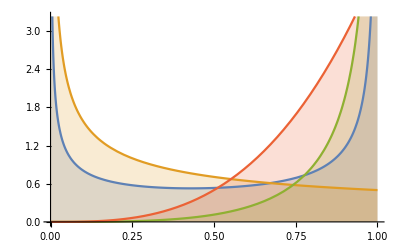

```mathematica
Plot[Table[PDF[BetaDistribution[α,b]],{α,{1/2, 4}}, {b, {1/3, 1}} ]//Evaluate,{x,0,1},Filling->Axis]
```

```mathematica
Функция распределения (Cumulative Distribution Function)
```

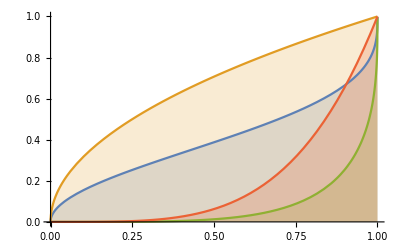

```mathematica
Plot[Table[CDF[BetaDistribution[α,b],x],{α,{1/2, 4}}, {b, {1/3, 1}} ]//Evaluate,{x,0,1},Filling->Axis]
```

```mathematica
A = {1/2, 4}
```

{1/2,4}

```mathematica
B = {1/3, 1}
```

{1/3,1}

```mathematica
M2[a_, b_] = a / (a + b)
```

a/(a+b)

```mathematica
Зависимость МатОжидания и Средней Наработки от параметров распределения
```

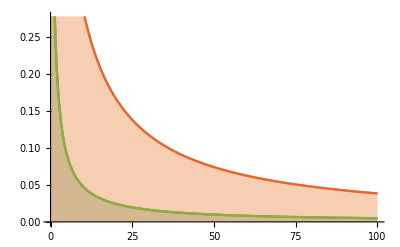

```mathematica
Plot[{Table[Mean[BetaDistribution[a,b]], {a, A}], Table[M2[a, b], {a, A}]}//Evaluate,{b,0,100},Filling->Axis]
```

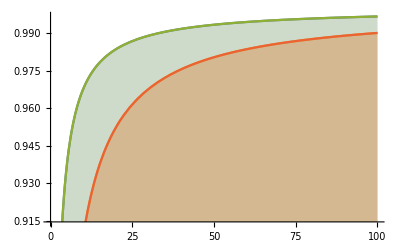

```mathematica
Plot[{Table[Mean[BetaDistribution[a,b]], {b, B}], Table[M2[a, b], {b, B}]}//Evaluate,{a,0,100},Filling->Axis]
```

```mathematica
Мода в зависимости от параметров распределения (для a, b >1)
mode[a_, b_] = (a-1)/(a+b-2)
```

в от Мода параметров зависимости распределения

(-1+a)/(-2+a+b)

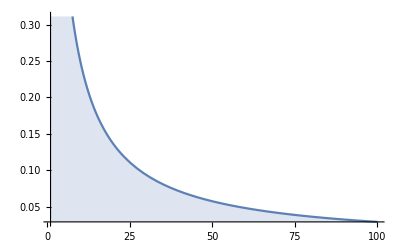

```mathematica
Plot[mode[4,b]//Evaluate,{b,1,100},Filling->Axis]
```

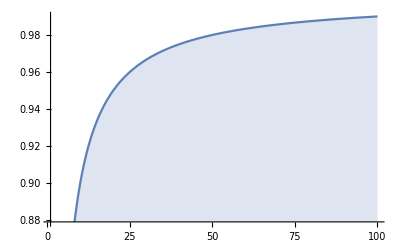

```mathematica
Plot[mode[a,2]//Evaluate,{a,1,100},Filling->Axis]
```

```mathematica
Медиана
```

```mathematica
Me[a_, b_] = (a - 1/3)/(a + b - 2/3)
```

(-1/3+a)/(-2/3+a+b)

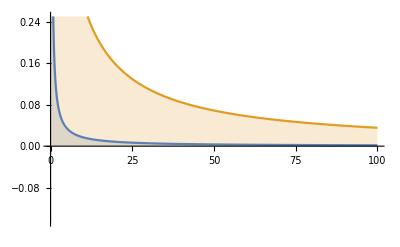

```mathematica
Plot[Table[Me[a,b], {a, A}]//Evaluate,{b,0,100},Filling->Axis]
```

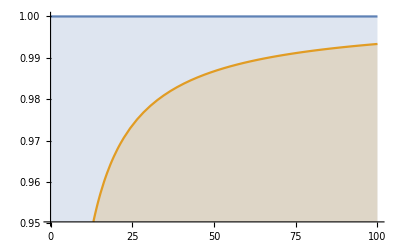

```mathematica
Plot[Table[Me[a,b], {b, B}]//Evaluate,{a,0,100},Filling->Axis]
```

```mathematica
СКО
```

```mathematica
Dev[a_, b_] = StandardDeviation[BetaDistribution[a, b]]
DevTableA[b_] = Table[Dev[a, b], {a,A}] 
DevTableB[a_] = Table[Dev[a, b], {b, B}]
```

(√a √b)/((a+b) √(1+a+b))

{(√b)/(√2 (1/2+b) √(3/2+b)),(2 √b)/((4+b) √(5+b))}

{(√a)/(√3 (1/3+a) √(4/3+a)),(√a)/((1+a) √(2+a))}

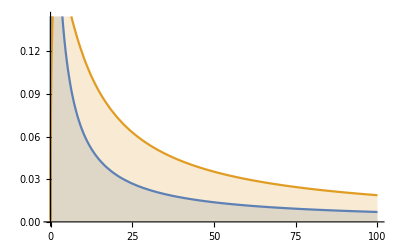

```mathematica
Plot[DevTableA[b]//Evaluate,{b,0,100},Filling->Axis]
```

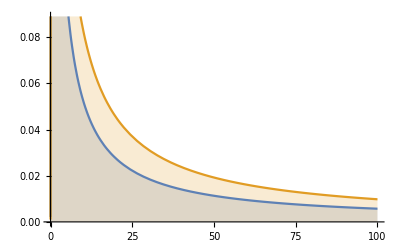

```mathematica
Plot[DevTableB[a]//Evaluate,{a,0,100},Filling->Axis]
```

```mathematica
Дисперсия
```

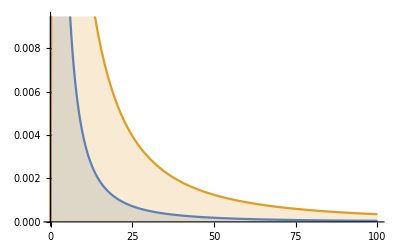

```mathematica
Plot[DevTableA[b]*DevTableA[b]//Evaluate,{b,0,100},Filling->Axis]
```

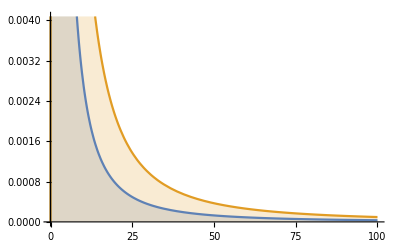

```mathematica
Plot[DevTableB[a]*DevTableB[a]//Evaluate,{a,0,100},Filling->Axis]
```

```mathematica
Коэффициент Асимметрии
```

```mathematica
assym[a_, b_] = 2*(b - a)*Sqrt(a+b+1)/((a+b+2)*Sqrt(a*b))
```

(2 (-a+b) (1+a+b))/(a b (2+a+b))

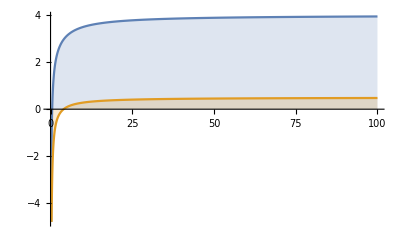

```mathematica
Plot[Table[assym[a,b], {a, A}]//Evaluate,{b,0,100},Filling->Axis]
```

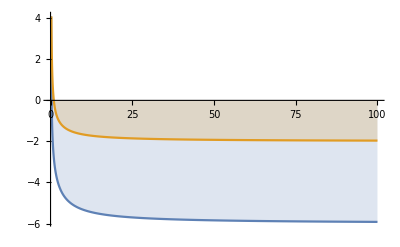

```mathematica
Plot[Table[assym[a,b], {b, B}]//Evaluate,{a,0,100},Filling->Axis]
```

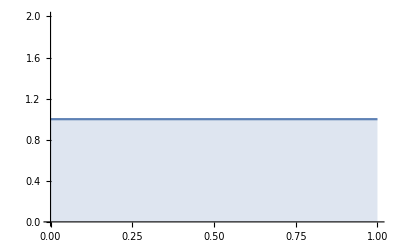

```mathematica
Plot[Table[PDF[BetaDistribution[α,b],x],{α,{1}}, {b, {1}} ]//Evaluate,{x,0,1},Filling->Axis]
```

```mathematica
Plot[PDF[BetaDistribution[α,b]],{α,{1}}, {b, {1}} ]//Evaluate,{x,0,1},Filling->Axis]
```